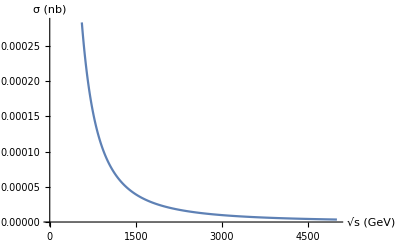

```mathematica
ListPlot[TableCross,Joined->True,AxesLabel-> {"√s (GeV)","σ (nb)"}]
```

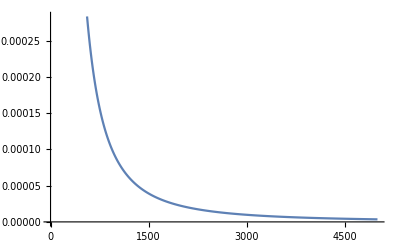

```mathematica
ListPlot[TableCross,Joined->True,Frame->{{Automatic,Automatic},{Automatic,Automatic}},FrameLabel-> {"\!\(\*SqrtBox[\(s\)]\) (GeV)","σ (nb)"}]
```

```mathematica
ListPlot[TableCross,Joined->True,FrameLabel->{"\!\(\*SqrtBox[\(s\)]\) (GeV)","σ (nb)"},Frame->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[Black,Thickness[Small]]]
```

-Graphics-

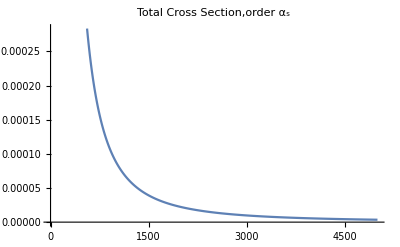

```mathematica
Show[%,PlotLabel->RawBoxes[RowBox[{RowBox[{"Total"," ","Cross"," ","Section"}],",",RowBox[{"order"," ",SubscriptBox["α","s"]}]}]],LabelStyle->{FontFamily->"Times",GrayLevel[0]},ImageResolution->2000]
```

```mathematica
Export["/Users/asight4soreyes/Desktop/Totaltest.png",%94,"PNG",ImageResolution->1000]
```

/Users/asight4soreyes/Desktop/Totaltest.png

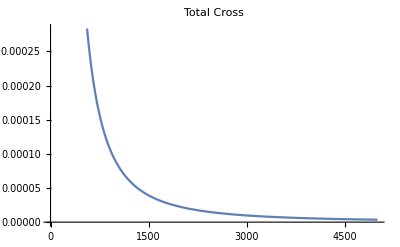

```mathematica
Show[%37,PlotLabel->HoldForm[Total Cross]]
```

```mathematica
ReleaseHold[Total Cross]
```

Cross Total

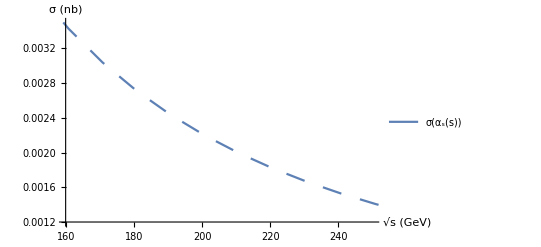

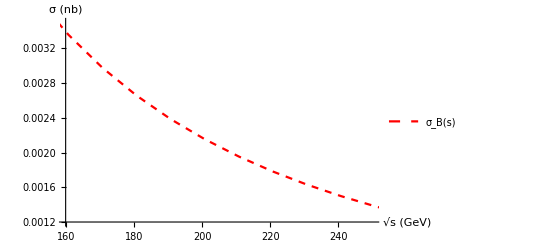

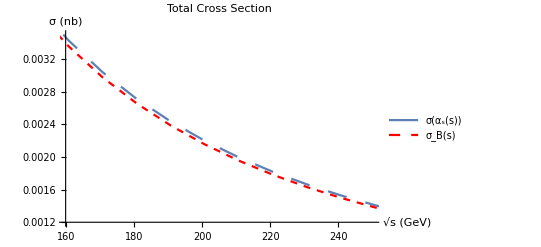

```mathematica
A2=ListPlot[TableCross2,Joined->True,AxesLabel-> {"√s  (GeV)","σ (nb)"},PlotStyle->{Dashing[Large]},PlotRange->{{160,250},{0.0012,0.0035}},PlotLegends->{"σ(α_s(s))",LabelStyle->{FontFamily->"Times",GrayLevel[0]}}]
B2=ListPlot[TableBorn,Joined->True,AxesLabel-> {"√s  (GeV)","σ (nb)"},PlotStyle->{Dashing[Small],Red},PlotRange->{{160,250},{0.0012,0.0035}},PlotLegends->{"σ_B(s)",LabelStyle->{FontFamily->"Times",GrayLevel[0]}}]
Show[A2,B2,PlotLabel->HoldForm[Total Cross Section],Frame->{{Automatic,Automatic},{Automatic,Automatic}},FrameLabel-> {"\!\(\*SqrtBox[\(s\)]\) (GeV)","σ (nb)"},LabelStyle->{FontFamily->"Times",GrayLevel[0]}]
```

```mathematica
Export["/Users/asight4soreyes/Desktop/CrossSectionComparisonGraph.png",%,"PNG",ImageResolution->500]
```

/Users/asight4soreyes/Desktop/CrossSectionComparisonGraph.png

γ^μ(g_V-g_A γ^5)